```mathematica
bookwinnersDataset=Import["C:\\Users\\hekim\\Box Sync\\wheaton\\Papers\\Works in Progress\\Testing 4.10 II.xlsx",{"Dataset",1},HeaderLines->1];
```

Convert the Dataset to its simplified form, a list of associations:

```mathematica
bookWinners=Normal[bookwinnersDataset]
```

{<|Year→2017.,Book Title→Juarez Girls Rising: Transformative Education in Times of Dystopia,Author→Claudia G.Cervantes-Soon,Academic Acknowledgements→Angela Valenzuela,Authors' Institution @ Publication→UNC, Chapel Hill,Author UG→UT, El Paso,Author PhD→UT, Austin,Publisher→University of Minnesota|>,2537,<|1|>}
 |  |  |  |

```mathematica
Dimensions@bookwinnersDataset
```

{2539,8}

```mathematica
First@bookwinnersDataset
```

Dataset[<>]

Delete the empty strings at level 2 (values of each association in the list) in bookwinners:
Delete “” => deletes the empty space in some of the columns and replaces it with a --

```mathematica
Dataset[bookWinnersClean=DeleteCases[bookWinners,"",{2}]];
```

Gather the rows by book titles to form “subtables”:

```mathematica
gatheredBookWinners=GatherBy[bookWinnersClean,#["Book Title"]&]
```

{{1},62}
 |  |  |  |

Display the gathered rows as a Dataset:
 For the year 2017 , “14 total” refers to the number of items in the grouping “2017”

```mathematica
gatheredBookWinners//Dataset
```

Dataset[<>]

Get the first subtable from gatheredBookWinners: (like using “sortyby in Excel”)
 “[[1]]” is taking the first list of association....

```mathematica
gatheredBookWinners[[1]]//Dataset;
```

Merge each of the subtables into a single row, collecting all distinct values of each key into a list:

```mathematica
?Merge
```

```mathematica
?Union
```

```mathematica
Dataset[mergedBookWinners=Merge[#,Union]&/@gatheredBookWinners];
```

Get the first element of each list of distinct values for all keys except “Academic Acknowledgements”:

Unlisting all colums except the academic acknowledgement column

```mathematica
Dataset[condensedBookWinners=MapIndexed[(If[
First[#2]===Key["Academic Acknowledgements"],
#1,
First[#1]
]&),#]&/@mergedBookWinners];
```

Dataset[<>]

Map Floor (Floor rounds the value down to lowest whole number) onto the value of each Year key to convert it to an integer:

```mathematica
Dataset[integerYearBookWinners=MapAt[Floor,condensedBookWinners,{All,Key["Year"]}]];
```

Taking all elements, starting from the 2nd row, and column 3

```mathematica
authors = integerYearBookWinners[[2;;,3]]
```

{Roberto G. Gonzales,Carla Shedd,Laurence Ralph,Nancy DiTomaso,Cybelle Fox,Shamus Rahman Khan,Mark Hunter,Mario Luis Small,Martín Sanchez-Jankowski,45,Jacqueline P. Wiseman,Laud Humphreys,Gerald D. Suttles,Elliot Liebow,Travis Hirschi and Hanan C. Selvin,Jerome H. Skolnick,Robert Boguslaw,David Matza}
 |  |  |  |

Accounting for co-authors

```mathematica
Select[authors,StringContainsQ[#," and "]&]
```

{John Hagan and Bill McCarthy,Melvin L. Oliver and Thomas M. Shapiro,Joyce Rothschild and J. Allen Whitt,Frances Fox Piven and Richard A. Cloward,Travis Hirschi and Hanan C. Selvin}
 |  |  |  |

Proof of concept of the function

```mathematica
StringSplit["John Hagan and Bill McCarthy"," and "]
```

{John Hagan,Bill McCarthy}

```mathematica
First@authors
```

Roberto G. Gonzales

```mathematica
StringSplit["Roberto G. Gonzales", " and "]
```

{Roberto G. Gonzales}

StringSplit Function is applied to column 3 (to split co-authors)

```mathematica
splitAuthors[authorString_String]:=StringSplit[authorString, " and "]
```

```mathematica
integerYearBookWinners//Take[#,3]&
```

{<|Year→2017,Book Title→Juarez Girls Rising: Transformative Education in Times of Dystopia,Author→Claudia G.Cervantes-Soon,Academic Acknowledgements→{Angela Valenzuela,12,Toni Avila},Authors' …blication→…,Author UG→UT, El Paso,Author PhD→UT, Austin,Publisher→University of Minnesota|>,<|1|>,<|1|>}
 |  |  |  |

```mathematica
Dataset[integerYearBookWinnersSplitAuthors=MapAt[splitAuthors,integerYearBookWinners,{All,"Author"}]]
```

Dataset[<>]

finding where this notebook is
Q: I am not sure how to create and what the “.m” function does?  When you import the .m file, it comes in evaluated

```mathematica
NotebookDirectory[]
```

C:\Users\hekim\Documents\WSS-Template\Final Project\Drafts FINAL PROJECT\

```mathematica
FileNameJoin[{NotebookDirectory[],"Up to Co-Authors.m"}]
```

C:\Users\hekim\Documents\WSS-Template\Final Project\Drafts FINAL PROJECT\Up to Co-Authors.m

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Up to Co-Authors.m"}],integerYearBookWinnersSplitAuthors]
```

C:\Users\hekim\Documents\WSS-Template\Final Project\Drafts FINAL PROJECT\Up to Co-Authors.m

```mathematica
integerYearBookWinnersSplitAuthors =Import[ "C:\\Users\\hekim\\Documents\\WSS-Template\\Final Project\\Drafts FINAL PROJECT\\Up to Co-Authors.m"]
```

{<|Year→2017,Book Title→Juarez Girls Rising: Transformative Education in Times of Dystopia,Author→{Claudia G.Cervantes-Soon},Academic Acknowledgements→{Angela Valenzuela,Aurolyn Luykx,11,Toni Avila},1,Author UG→UT, El Paso,Author PhD→UT, Austin,Publisher→University of Minnesota|>,61,<|1|>}
 |  |  |  |

### THE variable with the CLEAN DATA?

```mathematica
integerYearBookWinnersSplitAuthors
```

{<|Year→2017,Book Title→Juarez Girls Rising: Transformative Education in Times of Dystopia,Author→{Claudia G.Cervantes-Soon},Academic Acknowledgements→{Angela Valenzuela,Aurolyn Luykx,11,Toni Avila},1,Author UG→UT, El Paso,Author PhD→UT, Austin,Publisher→University of Minnesota|>,61,<|1|>}
 |  |  |  |

### These are alternative ways to select a single year or a range

```mathematica
bookWinnersForYear[year_]:=Select[integerYearBookWinnersSplitAuthors,#Year===year&]
```

```mathematica
bookWinnersBetweenYears[from_,to_]:=Select[integerYearBookWinnersSplitAuthors,Between[#Year,{from,to}]&]
```

```mathematica
bookWinnersForYear[1994]
```

{<|Year→1994,Book Title→What Machines Can't Do: Politics and Technology in the Industrial Enterprise,Author→{Robert Thomas},Academic Acknowledgements→{Bob Cole,Ed Schein,10,Tom Kochan,Tom Magnanti},1,Author UG→UC, Santa Cruz,Author PhD→Northwestern University,Publisher→University of California Press|>}
 |  |  |  |

```mathematica
bookWinnersBetweenYears[1994,1998]
```

{<|Year→1998,Book Title→The Making of the Unborn Patient: A Social Anatomy of Fetal Surgery,Author→{Monica J. Casper},Academic Acknowledgements→{Adele Clarke,41,William Liley},Aut…ion→…,Author UG→University of Chicago,Author PhD→UC, San Francisco,Publisher→Rutgers University Press|>,4,<|1|>}
 |  |  |  |

Per each book, create the edges, starting with one and then for all, and combine all of them
Use Values@ to drop the keys and just get the lists

```mathematica
Values@integerYearBookWinnersSplitAuthors[[1,{3,4}]]
```

{{Claudia G.Cervantes-Soon},{Angela Valenzuela,Aurolyn Luykx,Carol Brochin,Cecilia Balli,Douglas E. Foley,Elaine Hampton,Elizabeth Villareal,G. Sue Kasun ,Haydee Rodriguez,Keffrelyn Brown,Lourdes Diaz Soto,Luis Urrieta,Monica Neshyba,Toni Avila}}
 |  |  |  |

Proof of concept

```mathematica
Outer[DirectedEdge,{a,b,c},{4,5}]
```

{{a->4,a->5},{b->4,b->5},{c->4,c->5}}
 |  |  |  |

### Edges from winners Q5: I am not sure what “@@” and “/@” are doing? @@ replaced the head list and does the function

```mathematica
g@@f[5,6,7]
```

g[5,6,7]
 |  |  |  |

```mathematica
Plus@{1,2,3,4,5}
```

{1,2,3,4,5}
 |  |  |  |

```mathematica
Plus@@{1,2,3,4,5}
```

15

```mathematica
Plus@@{1,{2, 3},4,5}
```

{12,13}

```mathematica
edgesFromWinners[winners_]:=Join@@(Join@@Outer[DirectedEdge,Sequence@@Values@#]&)/@winners[[All,{3,4}]]
```

### All Years

```mathematica
edges=edgesFromWinners[integerYearBookWinnersSplitAuthors];
Length[edges]
```

2667

### Between Years - Enter the year ranges - Is this Disconnected Graph? It seems disconnected First line gets the Length, the second gets the Closeness Centrality score, ranked

```mathematica
edges=edgesFromWinners[bookWinnersBetweenYears[1994,1998]];
Length[edges]
```

406

```mathematica
First@edges
```

Monica J. Casper->Adele Clarke

```mathematica
edges=edgesFromWinners[bookWinnersBetweenYears[1994,1998]];
ClosenessCentrality[edges];
Sort[%,Greater]
```

{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,238,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
 |  |  |  |

```mathematica
VertexList[edges]
```

{Monica J. Casper,Adele Clarke,Anselm Strauss,Arsenio Comas,Barbara Koenig,Betty Levin,Bill Liley, Jr.,Bill Magee,Candace West,Craig Haney,David Becroft,302,John Van Maanen,Kent Bowen,Lotte Bailyn,Michael Unseem,Mike Piore,Paul Lagace,Paul Osterman,Rebecca Henderson,Rosanna Hertz,Tom Kochan,Tom Magnanti}
 |  |  |  |

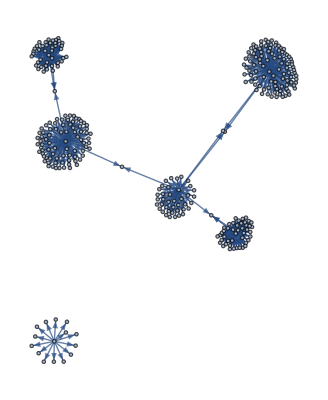

```mathematica
graph94to98=Graph[edges]
```

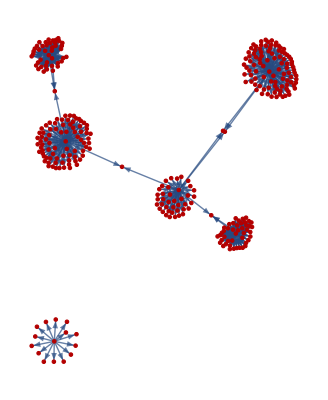

```mathematica
HighlightGraph[edges,VertexList[edges](*,VertexSize-> Thread[VertexList[edges]]*)]
```

```mathematica
?ConnectedComponents
```

Echoing just the length
ConnectedComponents returns vertex lists

```mathematica
ccVertices=ConnectedComponents[UndirectedGraph@graph94to98]//Echo[#,"",Length]&
```

2

{{Monica J. Casper,Adele Clarke,Anselm Strauss,Arsenio Comas,Barbara Koenig,Betty Levin,Bill Liley, Jr.,Bill Magee,Candace West,Craig Haney,289,Patricia Parker,Ron Gillis,Rose Labrador,Rosemary Gartner,Sara Eliesen,Shea Farrell,Tanis Abuda,Tina Sahay,Tracey-Ann Van Brenck,Zheng Wu},{1}}
 |  |  |  |

ConnectedGraphComponents returns graphs

2

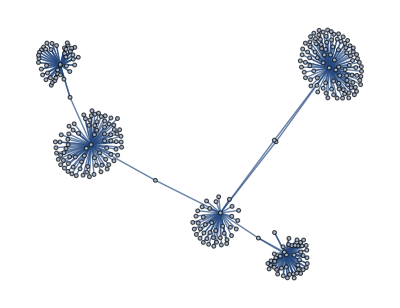
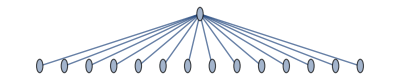

```mathematica
ccGraphs=ConnectedGraphComponents[UndirectedGraph@graph94to98]//Echo[#,"",Length]&
```

```mathematica
graph94to98giantComponent=First@ccGraphs
```

-Graphics-

```mathematica
EdgeList[graph94to98]//Length
```

406

```mathematica
First@EdgeList[graph94to98]
```

Monica J. Casper->Adele Clarke

```mathematica
Length/@%//Counts
```

Counts::invl: The argument 0->0 is not a list.

Counts[0->0]

### SIngle Year

```mathematica
edges=edgesFromWinners[bookWinnersForYear[1994]];
Length[edges]
```

14

### Data cleaning

testing if there is a missing person from acknowledgements - does not need to be evaluated
The names in the “author” column, and only this column, are surrounded by {}

```mathematica
integerYearBookWinners[[All,"Author"]]//Sort//Column
```

1
 |  |  |  |

```mathematica
Select[integerYearBookWinners[[All,{"Year","Academic Acknowledgements"}]],Length[#["Academic Acknowledgements"]]==0&]
```

{}

```mathematica
integerYearBookWinners[[All,"Year"]]
```

{2017,2016,2015,2014,2013,2012,2011,2010,2009,2008,2007,2006,2005,2004,2003,2002,2002,2001,2000,1999,1998,1997,1996,1995,1995,1994,1993,1992,1991,1990,1989,1989,1988,1988,1987,1986,1986,1986,1985,1984,1984,1983,1982,1981,1980,1979,1978,1977,1976,1975,1974,1973,1973,1972,1971,1970,1969,1968,1967,1967,1966,1965,1964}
 |  |  |  |

### FYI - Selecting a column, suppressed output

Column Five

```mathematica
authorsInstitution =Rest@bookwinnersDataset;
authorsInstitution[[All,5]];
```

Column Three

```mathematica
allAuthors =Rest@bookwinnersDataset;
authorsInstitution[[All,3]];
```

### Connecting Authors and Acknowledged

The graph does work with the new variable with Bob (07/01/19) and he helped me on this day to account for dual authorship

```mathematica
edges[[1]]//InputForm
```

DirectedEdge["Robert Thomas", "Bob Cole"]

### This is a complete graph including disconnected networks

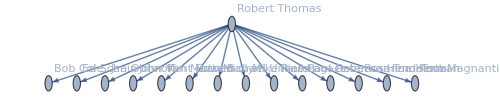

```mathematica
graph=Graph[edges, VertexLabels -> "Name",ImageSize -> 500]
```

### Remove disconnected networks (automated) In order to get the ConnectedComponents function to work, the graph had to be: 1) undirected, 2) ascertatin the main components, 3) use the Subgraph function, and 4) Use MaximalBy to take the largest length, and 5) take the “maincomponentvertices”

```mathematica
removeDisconnectedNetworks[edges_]:=Module[{
graph=Graph[edges, VertexLabels -> "Name",ImageSize -> 500],
components,
maincomponentvertices
},
components=ConnectedComponents[Graph[ReplaceAll[edges,DirectedEdge->UndirectedEdge], VertexLabels -> "Name",ImageSize -> 500]];
maincomponentvertices=MaximalBy[components,Length];
Subgraph[graph,maincomponentvertices]
]
```

### This is a graph with the disconnected networks removed

```mathematica
removeDisconnectedNetworks[edges]
```

-Graphics-

### Q7: I am not sure what this is doing - Is it even needed in this notebook or can it be removed?

```mathematica
graphsPerYearDisconnected=AssociationMap[
Graph[edgesFromWinners[bookWinnersForYear[#]], VertexLabels -> "Name",ImageSize -> 500]
&,Sort@integerYearBookWinnersSplitAuthors[[All,"Year"]]];
```

```mathematica
graphsPerYearDisconnected;
```

```mathematica
ClosenessCentrality/@graphsPerYearDisconnected
```

<|1964→{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},1965→{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},51,2017→{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}|>
 |  |  |  |

#### Without disconnected subgraphs

```mathematica
graphsPerYear=AssociationMap[
Graph[removeDisconnectedNetworks[edgesFromWinners[bookWinnersForYear[#]]], VertexLabels -> "Name",ImageSize -> 500]
&,Sort@integerYearBookWinnersSplitAuthors[[All,"Year"]]];
```

```mathematica
graphsPerYear;
```

```mathematica
ClosenessCentrality/@graphsPerYear
```

<|1964→{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},1965→{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},51,2017→{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}|>
 |  |  |  |

### Graphs for accumulating years (autogenerated)

```mathematica
yearsRange=MinMax[Sort@integerYearBookWinnersSplitAuthors[[All,"Year"]]]
```

{1964,2017}

#### With disconnected subgraphs

```mathematica
accumulatingGraphsDisconnected=AssociationMap[
Graph[edgesFromWinners[bookWinnersBetweenYears[yearsRange[[1]],#]], VertexLabels -> "Name",ImageSize -> 500]
&,Range@@yearsRange];
```

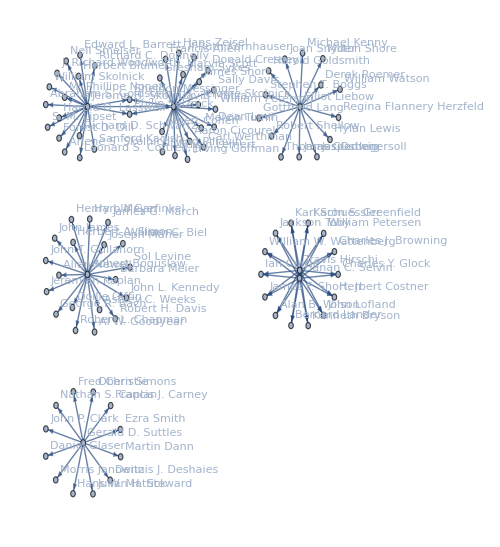

```mathematica
accumulatingGraphsDisconnected[1968]
```

```mathematica
ClosenessCentrality/@accumulatingGraphsDisconnected
```

<|1964→{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},52,2017→{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2368,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}|>
 |  |  |  |

#### Without disconnected subgraphs The main variable to run SNA metrics is “accumulatingGraphs”

```mathematica
graphsPerYear=AssociationMap[
Graph[removeDisconnectedNetworks[edgesFromWinners[bookWinnersForYear[#]]], VertexLabels -> "Name",ImageSize -> 500]
&,Sort@integerYearBookWinnersSplitAuthors[[All,"Year"]]];
```

```mathematica
accumulatingGraphs=AssociationMap[
Graph[removeDisconnectedNetworks[edgesFromWinners[bookWinnersBetweenYears[yearsRange[[1]],#]]], VertexLabels -> "Name",ImageSize -> 500]
&,Range@@yearsRange];
```

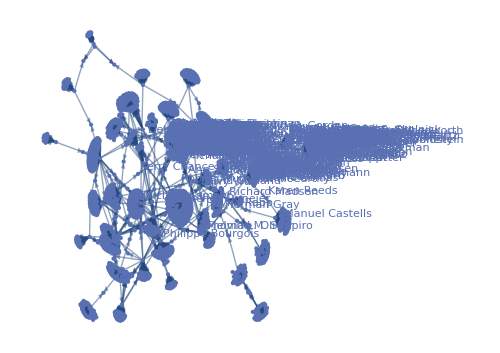

```mathematica
accumulatingGraphs[2017]
```

Change the Metric you want below:

```mathematica
Map[Module[{
highestDegreeVertex=VertexList[#][[Ordering[VertexOutDegree[#]][[-1]]]]
},
{highestDegreeVertex,VertexOutDegree[#,highestDegreeVertex]}
]&,accumulatingGraphs]//Dataset
```

Dataset[<>]

```mathematica
Dataset[<>]--m
```

The total number of years

```mathematica
Length@integerYearBookWinnersSplitAuthors[[All,1]]
```

63

The span of years to create a time series

```mathematica
integerYearBookWinnersSplitAuthors[[All,1]]//MinMax
```

{1964,2017}

### Time Series

```mathematica
v={2,1,6,5,7,4};
t={1,2,5,10,12,15};
ts=TimeSeries[v,{t}]
```

TimeSeries[…]

t = years
v = SNA metrics (in-degrees, SNA metrics, etc.)

TimeSeries[…]

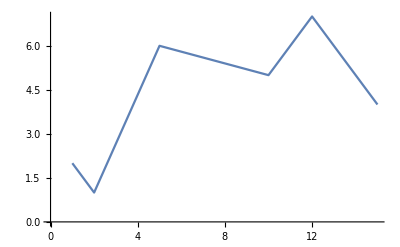

```mathematica
ListLinePlot[ts]
```

E. Which nodes or patterns (associations) emerge?

### Test (A Heuristic List)

A) Dunbar’s Rule	N = 150
B) Zipf’s		Kth is 1/k of the 1st number	(zipf distribution)
C) Sarnoff’s		V = n
D) Odlyzko’s		n log(n)
E) Metcalfe’s		V = n^2
F) Reed’s		V = 2^n
G) Feigenbaum	(x3-x2)/(x2-x1) = F Constant
Other rules/laws whereby I really start rambling into Neverland 
H) Cellular Automata?
I) Agent Based Modeling? 
J) Self-Organized Criticality?
K) Phase Transitions? 
L) Fractal Geometry
N) Built-in Mathematica tests?
O) Machine Learning tests?

### Visualizations

A. Highlight Key vertices or edges 
B. A Manipulate Function of time
Shortest Path?
CommunityGraphPlot (to show isolates?)

HOW come I cannot make a simple BARCHART?

Run this below so when you run tests it delimits output - doesn’t work!

```mathematica
SetOptions[EvaluationNotebook[],OutputSizeLimit->500]
```